```mathematica
(*Importing |C4| data*)
data=Import["/home/john/Documents/University/Years/Third-year/Semester 1/Modules/Labs/Acoustic Levitation/Acoustic Levitation/Analysis/Model Fitting/|C4|-shifted.csv"];
```

```mathematica
(*removing headers*)
data=Rest[data];
```

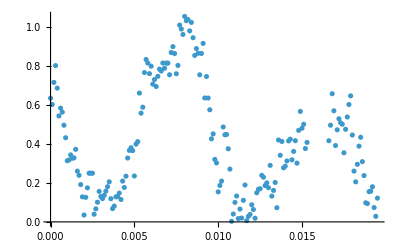

```mathematica
(*plotting raw data*)
ListPlot[data]
```

```mathematica
(*by-eye peak finding for exponential fit*)
dataPeaks={{0.0077,1.01},{0.0080,1.06},{0.0081,1.03},{0.0082,1.04},{0.0084,1.03},{0.0149,0.57},{0.168,0.66},{0.0169,0.57},{0.0177,0.54}}
```

{{0.0077,1.01},{0.008,1.06},{0.0081,1.03},{0.0082,1.04},{0.0084,1.03},{0.0149,0.57},{0.168,0.66},{0.0169,0.57},{0.0177,0.54}}

```mathematica
(*fitting exponential envelope*)
dataExp=NonlinearModelFit[
dataPeaks,
A*Exp[-beta*x],
{{A,1.81},{beta,38}},
x]
```

FittedModel[…]

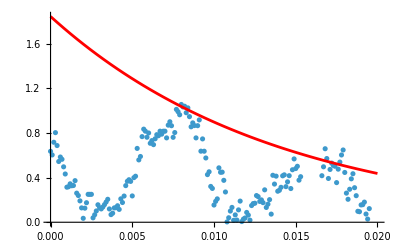

```mathematica
(*plotting for sanity check*)
Show[
ListPlot[data],
Plot[dataExp[x],{x,0,0.02},PlotStyle->Red],
PlotRange->Full
]
```

```mathematica
(*fitting decaying sinusoid*)
dataCos=NonlinearModelFit[
data,
1.84*Exp[-72*x]*Abs[Cos[omega*x+phi]],
{{omega,250},{phi}},
x];
```

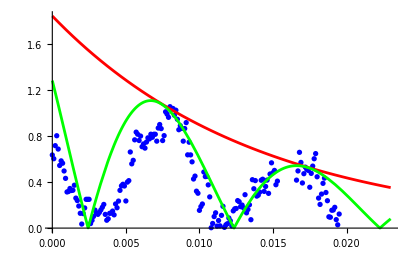

```mathematica
Show[
ListPlot[data,PlotStyle->Blue],
Plot[dataExp[x],{x,0,0.023},PlotStyle->Red],
Plot[dataCos[x],{x,0,0.023},PlotStyle->Green],
PlotRange->Full
]
```

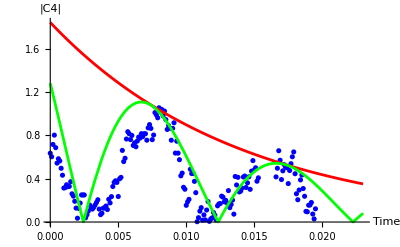

```mathematica
im=Show[%9,AxesLabel->{HoldForm[Time],RawBoxes[RowBox[{"|","C4","|"}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
(*Exporting graph*)
Export["mathematicaModelFitting.png",im,"PNG"]
```

mathematicaModelFitting.png

```mathematica
(*getting parameters and their errors*)
expParams=dataExp["BestFitParameters"];
expErrs=dataExp["ParameterErrors"];
fitParams=dataCos["BestFitParameters"];
fitErrs=dataCos["ParameterErrors"];
```

```mathematica
expParams
expErrs
fitParams
fitErrs
```

{A→1.8443,beta→71.9844}

{0.6045,33.4275}

{omega→316.748,phi→0.799554}

{5.46161,0.0338152}